```mathematica
Charting`$InteractiveHighlighting=False
```

False

## Coarse mesh with 14 samples

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/output``.csv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,11]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,11]//Evaluate,Range[1,11]}]//Association]&/@{"Up","Down"};
```

```mathematica
data2=Table[Transpose[{Range[0.75,4,0.25],di[All,ToString@StringForm["Band ``",#]]}//Normal]&/@Range[1,11],{di,data}];
```

```mathematica
Range[0.75,4,0.25]//Length
```

14

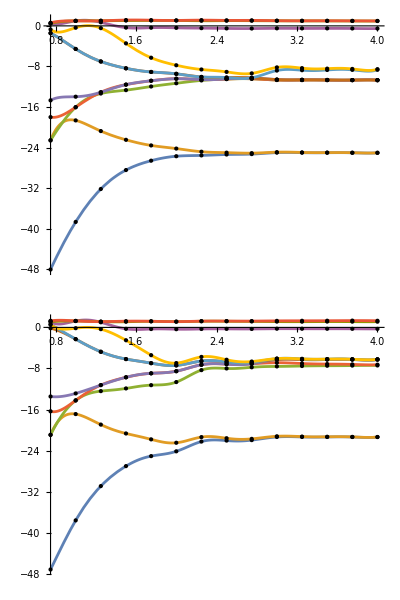

```mathematica
Table[Interpolation[#,InterpolationOrder->5,Method->"Spline"][d]&/@di//Plot[#,{d,0.75,4},ImageSize->Large,Epilog->{Point[#]&/@di},PlotRange->All]&,{di,data2}]//TableForm
```

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/outputETOT.csv"],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,1]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,1]//Evaluate,Range[1,1]}]//Association]
```

```mathematica
data2=Transpose[{Range[0.75,4,0.25],data[All,ToString@StringForm["Band ``",#]]}//Normal]&/@Range[1,1]//First
```

{{0.75,24.4871},{1.,-6.15164},{1.25,-9.83918},{1.5,-8.4155},{1.75,-6.39093},{2.,-4.68474},{2.25,-4.23425},{2.5,-3.94909},{2.75,-3.70156},{3.,-3.72284},{3.25,-3.75421},{3.5,-3.76573},{3.75,-3.76886},{4.,-3.77241}}

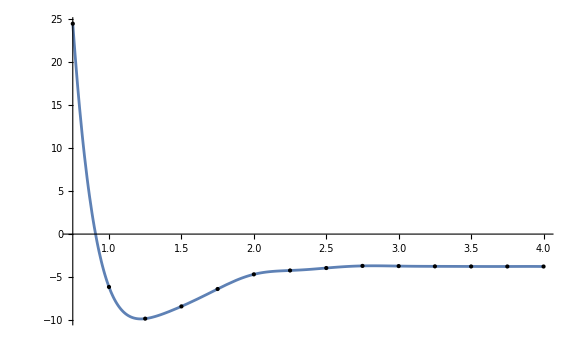

```mathematica
Interpolation[data2,InterpolationOrder->5,Method->"Spline"][d]//Plot[#,{d,0.75,4},ImageSize->Large,Epilog->{Point[#]&/@data2},PlotRange->All]&
```

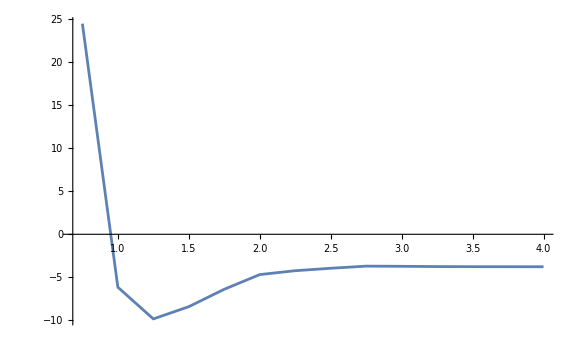

```mathematica
ListLinePlot[data2,PlotRange->All,ImageSize->Large]
```

## Finer mesh with 80 samples

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/output``.csv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,11]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,11]//Evaluate,Range[1,11]}]//Association]&/@{"FineUp","FineDown"};
```

```mathematica
data=Table[Transpose[{Range[0.05,4.0,0.05],di[All,ToString@StringForm["Band ``",#]]}//Normal]&/@Range[1,11],{di,data}];
```

```mathematica
Range[0.05,4.0,0.05]//Length
```

80

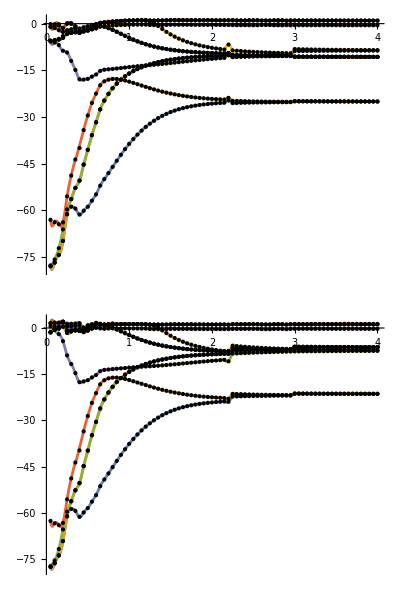

```mathematica
Table[Interpolation[#,InterpolationOrder->5,Method->"Spline"][d]&/@di//Plot[#,{d,0.05,4},Epilog->{PointSize[Small],Point[#]&/@di},ImageSize->Large,PlotRange->All]&,{di,data}]//TableForm
```

## Ultra-fine mesh with 400 samples

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/output``.csv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,11]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,11]//Evaluate,Range[1,11]}]//Association]&/@{"UltraFineUp","UltraFineDown"};
```

```mathematica
data=Table[Transpose[{Range[0.01,4.0,0.01],di[All,ToString@StringForm["Band ``",#]]}//Normal]&/@Range[1,11],{di,data}];
```

```mathematica
Range[0.01,4.0,0.01]//Length
```

400

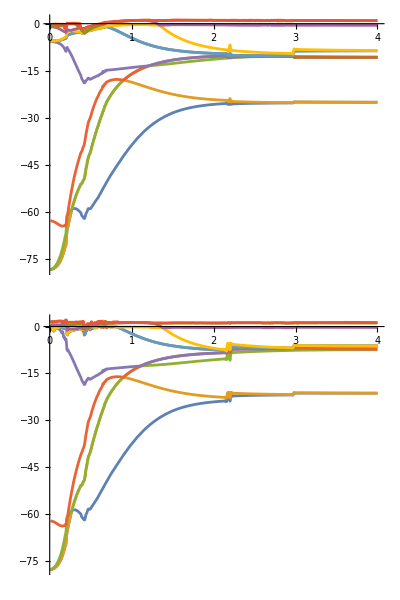

```mathematica
Table[Interpolation[#,InterpolationOrder->5,Method->"Spline"][d]&/@di//Plot[#,{d,0.01,4},ImageSize->Large,PlotRange->All]&,{di,data}]//TableForm
```

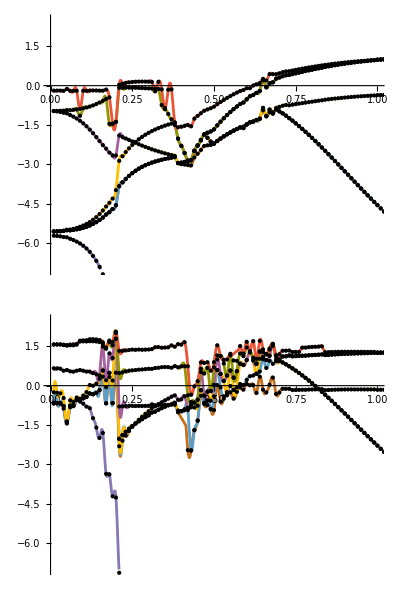

```mathematica
Table[Interpolation[#,InterpolationOrder->5,Method->"Spline"][d]&/@di//Plot[#,{d,0.01,1},Epilog->{PointSize[Small],Point[#]&/@di},ImageSize->Large,PlotRange->{-7,2.5}]&,{di,data}]//TableForm
```

## Mega-zoom into the interval [0, 1] with 1000 samples

```mathematica
Range[0.001,1.0,0.001]//Length
```

1000

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/output``.csv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,11]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,11]//Evaluate,Range[1,11]}]//Association]&/@{"MegaFineUp","MegaFineDown"};
```

```mathematica
data=Table[Transpose[{Range[0.001,1.0,0.001],di[All,ToString@StringForm["Band ``",#]]}//Normal]&/@Range[1,11],{di,data}];
```

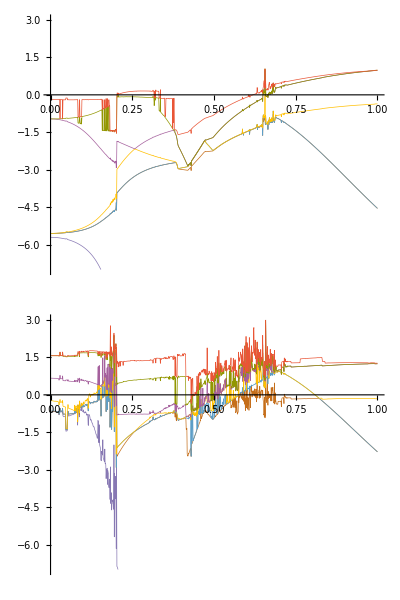

```mathematica
ListLinePlot[#,ImageSize->Full,PlotStyle->AbsoluteThickness[0.5],PlotRange->{-7,3}]&/@data//TableForm
```